## Setup

### PDE solver

```mathematica
ClearAll@runTwoComponentSim;
Options[runTwoComponentSim]=Join[Options[NDSolve],{"GridPoints"->100,"BC"->"Reflective"}];
runTwoComponentSim[f_,params_,{nInit_,etaInit_},tMax_,opts:OptionsPattern[]]:=First@NDSolve[{
D[n[x,t],t]==Dv D[eta[x,t],{x,2}],D[eta[x,t],t]==Dv (1+Du/Dv) D[eta[x,t],{x,2}]-Du D[n[x,t],{x,2}]-(f/.{n->n[x,t],η->eta[x,t]}),
If[OptionValue["BC"]==="Periodic",
{(* periodic BCs *)
n[0,t]==n[L,t],eta[0,t]==eta[L,t],(D[n[x,t],x]/.x->0)==(D[n[x,t],x]/.x->L),(D[eta[x,t],x]/.x->0)==(D[eta[x,t],x]/.x->L)
},
{(* no-flux BCs *)
(D[n[x,t],x]/.x->0)==0,(D[eta[x,t],x]/.x->0)==0,(D[n[x,t],x]/.x->L)==0,(D[eta[x,t],x]/.x->L)==0
}
],
(* initial condition *)
n[x,0]==nInit[x],
eta[x,0]==etaInit[x]
}/.params,
{n,eta},
{x,0,L/.params},
{t,0,tMax},
Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},(*Choose higher scale factor to enforce boundary conditions in case the initial condition does not fulfil them*)"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->1},"Method"->{"IDA","ImplicitSolver"->"Newton"}}
];
```

### Finite difference setup

Mass-conserving two-component reaction diffusion system using n=m+c,η=c+m D_u/D_v as variables.

#### Stationary state equations

```mathematica
discreteLaplace[data_,dx_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,2]/dx^2
]
```

```mathematica
ClearAll@setupFiniteDifferenceEqs;
setupFiniteDifferenceEqs[f_,gridRes_]:=With[{
nVec=Thread[n@Range[gridRes]],
etaVec=Thread[eta@Range[gridRes]]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"nVec"->nVec,
"Vars"->Join[nVec,{eta}],
"Eqs"->{
Du discreteLaplace[nVec,L/gridRes]+(f/.{n->nVec,η->eta}),
Total@nVec-gridRes nbar
}
|>
]
```

```mathematica
getInitGuess[fdSetup_,params_,initSol_]:=Join[
Transpose[{
fdSetup["nVec"],
n[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
{{eta,eta[0,T]/.params/.initSol}}
]
```

#### Jacobian for anti-symmetric coarsening mode of two symmetrically “glued” stationary states

```mathematica
laplaceMatrixAS[n_]:=SparseArray[{
{1,1}->-1,{-1,-1}->-3,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]
```

```mathematica
Options@constructGluedJacobianAS={"Reverse"->False};
constructGluedJacobianAS[fdSetup_,params_,statSol_,dfdu_,OptionsPattern[]]:=
With[{
solVec=If[OptionValue["Reverse"]===True,Reverse@#,#]&@Transpose[{
fdSetup["nVec"]/.statSol,
ConstantArray[eta/.statSol,Length@statSol-1]
}],
dfduP=dfdu/.params,
gridRes=Length@statSol-1
},
KroneckerProduct[laplaceMatrixAS[gridRes],{{0,Dv},{-Du,Dv(1+Du/Dv)}}/(L/gridRes)^2/.params]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{n,η}->solVec[[i]]]),
{i,gridRes}
]
]
]
```

### Model setup

Cubic reation kinetics in (n,η) variables

```mathematica
f=η-n^3+n;
```

```mathematica
fixedParams={nbar->-2/10,Dv->10,Du->1,L->20,T->100};
params=Join[{Dv->10},fixedParams];
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[f,200];
```

## Stationary state

```mathematica
initRun=runTwoComponentSim[
f,
params,
{
nbar+0.5Cos[Pi#/L]&,
0&
},
T/.fixedParams
];
```

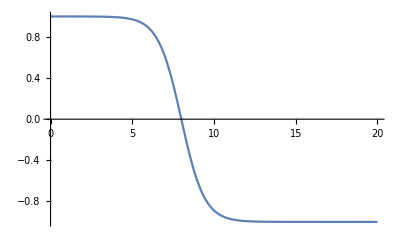

```mathematica
Plot[n[x,T/.params]/.initRun,{x,0,L/.params}]
```

```mathematica
statSol=Block[{n,eta},FindRoot[
fdSetup["Eqs"]/.params,
getInitGuess[fdSetup,params,initRun],
MaxIterations->100,
WorkingPrecision->100,
AccuracyGoal->20,
PrecisionGoal->20
]
];//AbsoluteTiming
```

{0.204374,Null}

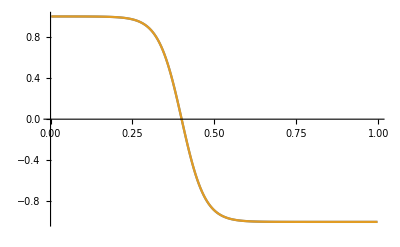

```mathematica
ListLinePlot[{
Transpose[{x,n[L x,T]/.params/.initRun}/.x->fdSetup["UnitGrid"]],
Transpose[{fdSetup["UnitGrid"],fdSetup["nVec"]/.statSol}]
},
PlotRange->All
]
```

## Linear stability analysis

#### Analytic expression for growth rate in diff- and react-limited regimes

```mathematica
σR=48 Exp[-2ξ L/√(Du/2)];
σD=8 Dv/(√(Du/2) L(1-ξ))Exp[-2ξ L/√(Du/2)]/.ξ->(nbar+1)/2;
```

#### Finite difference Jacobian construction, usage example

```mathematica
SetPrecision[
Re@Eigenvalues[Normal@constructGluedJacobianAS[
fdSetup,
params,
statSol,
D[{0,-f},{{n,η}}]
],-1,Method->{"Arnoldi","Tolerance"->10^-20}][[1]],
10
]//AbsoluteTiming
```

{0.607822,1.229327885×10^-9}

### D_v-sweep

Note: the stationary state for the cubic model is independent of D_v. Therefore, we only need to calculate the leading eigenvalue for each D_v.

```mathematica
evSweep=Table[{
DvIter,
SetPrecision[Re@Eigenvalues[Normal@constructGluedJacobianAS[
fdSetup,
Join[{Dv->SetPrecision[DvIter,100]},params],
statSol,
D[{0,-f},{{n,η}}]
],-1,Method->{"Arnoldi","Tolerance"->10^-20}][[1]],10]
},
{DvIter,10^Range[0,4.9,0.2]}
];//AbsoluteTiming
```

{15.1825,Null}

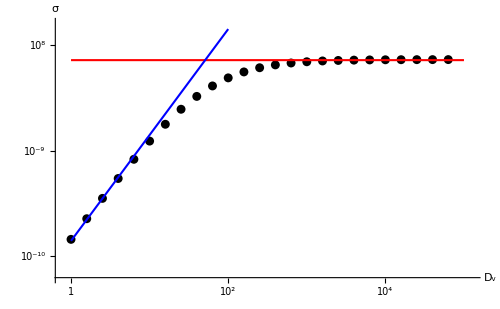

```mathematica
Show[
ListPlot[Log10@evSweep,PlotStyle->Black],
Graphics[{
AbsoluteThickness[1.5],
Red,
Line[{{0,#},{5,#}}&@(Log10@σR/.params)],
Blue,
Line[{{0,Log10@σD/.Dv->1},{2,Log10@σD/.Dv->100}}/.params]
}],
AxesOrigin->{-0.2,-10.2},
PlotRange->{{-0.1,5.1},{-10.2,-7.8}},
Ticks->{
{{0,1},{2,"10^2"},{4,"10^4"}},
{{-10,"10^-10"},{-9,"10^-9"},{-8,"10^8"}},
},
BaseStyle->{Black,14},
AxesLabel->{Subscript[D, v],σ},
ImageSize->500
]
```